```mathematica
Plotting skyrmions 

X = 1; Y =1;
scZ = 0.5;  (*height superconductor*)
fmZ= 0.2; (*heigh of ferromagnet*)

g1 = Graphics3D[{ 
{Specularity[0.1],Opacity[0.2],Gray,Lighting->{{"Ambient",Gray}},Cuboid[{-X,-1.3Y,-scZ},{X,Y,0}]}, (*bottom rectangle - superconductor*)
{Specularity[0.1],Opacity[0.1],Blue,Lighting->{{"Ambient",Blue}},Cuboid[{-X,-1.3Y,0},{X,Y,fmZ}]}        (*top rectangle - ferromagnet*)
},Boxed->False(*ViewPoint->{40000,-60000,70000}*)];

(*define and plot skyrmion field*)
R = 3 X/4; (*radius of skyrmion*)
θ[x_,y_]:= π(1-Exp[-(x^2+y^2)/R^2]); (*Polar angle*)
t =0; (*Skyrmion of the first kind -> t=0; Skyrmion of the second kind -> t=1 *)


(*cos and sin of azimuthal angle*)
cosϕ[x_,y_ ]:= ((1-t )x-t y)/(√(x^2+y^2)); sinϕ[x_,y_]:= ((1-t) y+t x)/(√(x^2+y^2)); 


g2 = VectorPlot3D[{cosϕ[x,y ]Sin[θ[x,y]],sinϕ[x,y ]Sin[θ[x,y]],Cos[θ[x,y]]},{x,-X,X},{y,- Y,Y},{z,fmZ/2,fmZ/2+0.01},VectorScale->0.11,VectorPoints->10,VectorStyle->{Blue,"Arrow3D"},VectorColorFunction->Function[{x,y,z,vx,vy,vz,n},ColorData["TemperatureMap"][Exp[-7((x-.5)^2+(y-.5)^2)]]]];

Show[g1,g2] (*plot all  figures *)
```

Plotting skyrmions

-Graphics3D-

```mathematica
table=Import["localized.dat","Table",Path-> "C:\\Users\\pershoguba\\Dropbox\\Research\\Skyrmion-Project\\skyrmion-ysr\\Figures"];
baddata[entry_]:=Not[MatchQ[entry,{_?NumberQ,_?NumberQ,_?NumberQ}]];
refinedData=DeleteCases[table,_?baddata];
ListPlot3D[refinedData,BoxRatios->{1,1,1},PlotRange-> {{35,65},{35,65},{0,0.005}},ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
table
```

Import[localized.dat,Path→C:\Users\pershoguba\Dropbox\Research\Skyrmion-Project\skyrmion-ysr\Figures,Table]

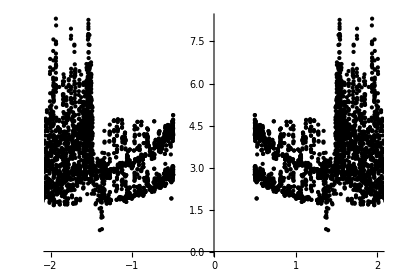

```mathematica
aspRatio = 0.7;
table=Import["psi4.dat","Table",Path-> "C:\\Users\\pershoguba\\Dropbox\\Research\\Skyrmion-Project\\skyrmion-ysr\\Figures"];
baddata[entry_]:=Not[MatchQ[entry,{_?NumberQ,_?NumberQ,_?NumberQ}]];
refinedData=DeleteCases[table,_?baddata];
ListPlot[table,PlotStyle-> Black,AspectRatio->aspRatio ,TicksStyle-> Directive[18],PlotRange->{{-2,2}}]
```

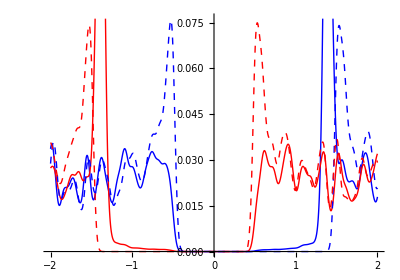

```mathematica
aspRatio = 0.7;
ldosupSkyrm=Import["ldosUp-skyrmion.dat","Table",Path-> "C:\\Users\\pershoguba\\Dropbox\\Research\\Skyrmion-Project\\skyrmion-ysr\\Figures"];
ldosdownSkyrm=Import["ldosDown-skyrmion.dat","Table",Path-> "C:\\Users\\pershoguba\\Dropbox\\Research\\Skyrmion-Project\\skyrmion-ysr\\Figures"];
ldosupOff=Import["ldosUp-Off.dat","Table",Path-> "C:\\Users\\pershoguba\\Dropbox\\Research\\Skyrmion-Project\\skyrmion-ysr\\Figures"];
ldosdownOff=Import["ldosDown-Off.dat","Table",Path-> "C:\\Users\\pershoguba\\Dropbox\\Research\\Skyrmion-Project\\skyrmion-ysr\\Figures"];

ListLinePlot[{ldosupSkyrm,ldosdownSkyrm,ldosupOff,ldosdownOff},PlotStyle-> {{Thick,Blue},{Thick,Red},{Dashed,Thick,Blue},{Dashed,Thick,Red}},AspectRatio->aspRatio ,TicksStyle-> Directive[18]]
```

```mathematica
R =3 X/8;
g5 =VectorPlot3D[{cosϕ[x,y ]Sin[θ[x,y]],sinϕ[x,y ]Sin[θ[x,y]],Cos[θ[x,y]]},{x,-X,X},{y,- Y,Y},{z,fmZ/2,fmZ/2+0.01},VectorScale->0.05,VectorPoints->19,VectorStyle->{Blue,"Arrow3D"},VectorColorFunction->Function[{x,y,z,vx,vy,vz,n},ColorData["TemperatureMap"][Exp[-40((x-.5)^2+(y-.5)^2)]]],Boxed->False,Axes -> False,BoxRatios->{1,1,0.03},RegionFunction->Function[{x,y,z},x^2+y^2<0.5]];
Show[g5]
```

-Graphics3D-

```mathematica
R =X/20;
g3 = VectorPlot3D[{cosϕ[x,y ]Sin[θ[x,y]],sinϕ[x,y ]Sin[θ[x,y]],Cos[θ[x,y]]},{x,-X,X},{y,- Y,Y},{z,fmZ/2,fmZ/2+0.01},VectorScale->0.05,VectorPoints->19,VectorStyle->{Blue,"Arrow3D"},VectorColorFunction->Function[{x,y,z,vx,vy,vz,n},ColorData["TemperatureMap"][Exp[-1000((x-.5)^2+(y-.5)^2)]]],Boxed->False,Axes -> False,BoxRatios->{1,1,0.03},RegionFunction->Function[{x,y,z},x^2+y^2<0.5]];
g4 = Graphics3D[ 
{Red,Arrowheads[0.1],Arrow[Tube[{{0,0,0},{0,0,0.4}},0.03]]   },Boxed->False(*ViewPoint->{40000,-60000,70000}*)];
Show[g4,g3]
```

-Graphics3D-

```mathematica
Determining Se and Sm from the skyrmion field
```

```mathematica
R  = 1;
θ[r]:= π(1-Exp[-r^2/R^2]); (*Azimuthal angle*)
Integrate[2π r (Cos[θ[r]]+1),{r,0,Infinity}]
SeCoefficient=%//N
Sm = Integrate[2π r^2 Sin[θ[r]],{r,0,Infinity}]
SmCoefficient=%//N
```

π (EulerGamma-CosIntegral[π]+Log[π])

5.17822

∫_0^∞ 2 π r^2 Sin[(1-ⅇ^(-r^2)) π]ⅆr

6.53068

```mathematica
Simplify[∫_0^∞ 2 π r^2 Sin[(1-ⅇ^(-r^2)) π]ⅆr]
```

∫_0^∞ 2 π r^2 Sin[ⅇ^(-r^2) π]ⅆr

{-1.21872,-1.21872,-0.5,-0.5,0.5,0.5,1.21872,1.21872}

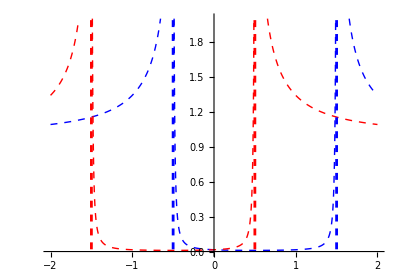

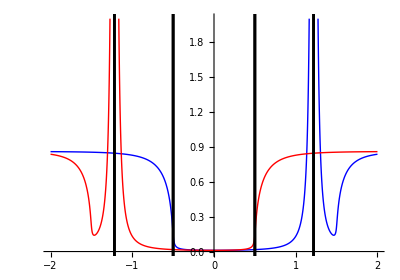

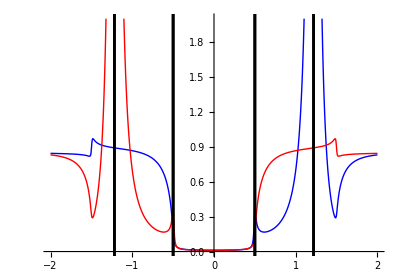

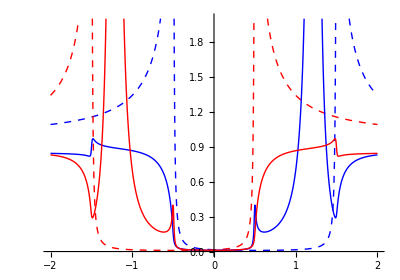

```mathematica
Plotting  LDOS near the skyrmion ;
id =({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});σx=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}) ; σy=({{0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}}); σz =({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}); τx = ({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}}); τz =({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
EF = 1; p =1; ρ= 1/(4π);  (*Fermi energy and momentum fix DOS*)
Δ = 0.1EF;S = 0.5Δ;  (*Gap and external magnetization*)
R =2.5;  Se = R^2 S SeCoefficient; Sm = 0.1 R^3 S SmCoefficient;(*Parameters of skyrmion: size and effective out-of-plane spin, effective in-plane monopole moment*)

 X =Se π ρ;  ES =  (1-X^2)/(1+X^2);  (*position of conventional YSR state*)
Γ= 0.001; (*imaginary infinitesimal*)
ClearAll["ω","LDOS","G","barG"]

G[ω_]:=-π ρ ((id+σz)/2) .(((ω+ⅈ Γ-S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ-S)^2)))-π ρ ((id-σz)/2) .(((ω+ⅈ Γ+S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ+S)^2)));
barG[ω_]:= -π ρ ((id-σz)/2) .(((ω+ⅈ Γ-S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ-S)^2)))-π ρ ((id+σz)/2) .(((ω+ⅈ Γ+S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ+S)^2)));
T[ω_]:=Inverse[id+Se σz.G[ω]-Sm^2 p^2 G[ω].barG[ω]].(-Se σz+Sm^2 p^2 barG[ω]);
T0[ω_]:=Inverse[id+Se σz.G[ω]].(-Se σz);

LDOSσ[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).(G[ω]+G[ω].T[ω].G[ω])]];
LDOSσ0[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).(G[ω]+G[ω].T0[ω].G[ω])]];
LDOSσAwayFromSkyrmion[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).G[ω]]];


Solution for the  T-matrix poles;


ClearAll["ω","g","barg"]
g=-π ρ ((id+σz)/2) .(((ω-S)id +Δ τx)/(√(Δ^2-(ω-S)^2)))-π ρ ((id-σz)/2) .(((ω+S)id +Δ τx)/(√(Δ^2-(ω+S)^2)));
barg  = -π ρ ((id-σz)/2) .(((ω-S)id +Δ τx)/(√(Δ^2-(ω-S)^2)))-π ρ ((id+σz)/2) .(((ω+S)id +Δ τx)/(√(Δ^2-(ω+S)^2)));
(*Find determinant and find roots*)
ListOfTmatrixPoles=(ω/.Solve[ Simplify[Det[id+Se σz.g]]==0,ω])/Δ//Re 

Preparation before plotting ;

maxY = 2; (* PlotRange/.AbsoluteOptions[gr1,PlotRange] //Flatten//Last;*)
VerticalLine [ω_] :=Line[{{ω,-0.1},{ω,maxY +0.1}}]; (*define auxiliarly function*)
aspRatio = 0.7;




Plot LDOS for pure ferromagnet ;
gr1 = Plot[{LDOSσAwayFromSkyrmion[Δ ω,σz]/ρ,LDOSσAwayFromSkyrmion[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Dashed,Blue},{Thick, Dashed,Red}},
TicksStyle-> Directive[18],AspectRatio->0.7,PlotRange->{{-2,2},{0,maxY}}];
gr1a = Graphics[{Blue,Dashed,Thickness[0.005],VerticalLine /@ {1+S/Δ,-1+S/Δ},Red,VerticalLine /@ {1-S/Δ,-1-S/Δ}}];
Show[gr1,gr1a]

Plot LDOS for skyrmion with simple T-matrix     ;
gr2 = Plot[{LDOSσ0[Δ ω,σz]/ρ,LDOSσ0[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Blue},{Thick, Red},{Thick,Blue,Thickness[0.005],Dashing[0.05]},{Thick, Red,Thickness[0.005],Dashing[0.05]},{Thick, Black},{Thickness[0.01],Dashing[0.05],Green//Darker}},
TicksStyle-> Directive[18],AspectRatio->aspRatio,PlotRange->{{-2,2},{0,maxY}},MaxRecursion->6];
gr2a = Graphics[{Blue,(*Dashed,*)Thickness[0.005],(*VerticalLine /@ {1+S/Δ,-1+S/Δ},Red,VerticalLine /@ {1-S/Δ,-1-S/Δ},*)Black,VerticalLine/@ ListOfTmatrixPoles}];
Show[gr2,gr2a]

Plot LDOS for skyrmion with modified T-matrix     ;

gr3 = Plot[{LDOSσ[Δ ω,σz]/ρ,LDOSσ[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Blue},{Thick, Red},{Thick, Black},{Thickness[0.01],Dashing[0.05],Green//Darker}},
TicksStyle-> Directive[18],AspectRatio->aspRatio,PlotRange->{{-2,2},{0,maxY}},MaxRecursion->4];

Show[gr3,gr2a]
Show[gr1,gr3]
```

```mathematica
u
```

```mathematica
N[1/(2π)]
```

```mathematica
E
```

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
Integrate[Sin[x]/x Sin[x/3]/(x/3),{x,0,Infinity}]
Integrate[Sin[x]/x Sin[x/3]/(x/3)Sin[x/5]/(x/5),{x,0,Infinity}]
Integrate[Sin[x]/x Sin[x/3]/(x/3)Sin[x/5]/(x/5)Sin[x/6]/(x/6),{x,0,Infinity}]

Integrate[Sin[x]/x Sin[x/3]/(x/3)Sin[x/5]/(x/5)Sin[x/7]/(x/7)Sin[x/9]/(x/9)Sin[x/11]/(x/11)Sin[x/13]/(x/13)Sin[x/15]/(x/15),{x,0,Infinity}]
```

π/2

π/2

π/2

«1 more identical outputs»

(467807924713440738696537864469 π)/935615849440640907310521750000

```mathematica
1/3+1/5+1/7+1/9+1/11+1/13+1/15
```

46027/45045

```mathematica
FullSimplify[Integrate[(Cos[a Cos[ϕ]]Exp[ - b Cos[ϕ]])/(2 π),{ϕ,-π/2,π/2}, Assumptions->a>0&&b>0]]
```

Integrate[(ⅇ^(-b Cos[ϕ]) Cos[a Cos[ϕ]])/(2 π),{ϕ,-π/2,π/2},Assumptions→a>0&&b>0]

```mathematica
Integrate[(Exp[(ⅈ  a - b)  Sin[ϕ]]-Exp[(-ⅈ  a - b)  Sin[ϕ]])/(2π),{ϕ,0,π},Assumptions-> a>0 && b>0]
```

1/2 (-BesselJ[0,a-ⅈ b]+BesselJ[0,a+ⅈ b]+ⅈ StruveH[0,a-ⅈ b]+ⅈ StruveH[0,a+ⅈ b])

```mathematica
1/2 (BesselJ[0,a-ⅈ b]+BesselJ[0,a+ⅈ b]-ⅈ StruveH[0,a-ⅈ b]+ⅈ StruveH[0,a+ⅈ b])
```

```mathematica
%//FullSimplify
```

```mathematica
f[a_,b_]:=1/2 (BesselJ[0,(pF-ⅈ pX)/x]+BesselJ[0,(pF+ⅈ pX)/x]-ⅈ StruveH[0,(pF-ⅈ pX)/x]+ⅈ StruveH[0,(pF+ⅈ pX)/x]);
Expand
```

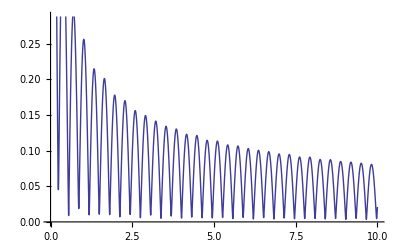

```mathematica
Plot[Abs[N[f[10x,ⅈ x]]],{x,0,10}]
```

```mathematica
Series[1/2 (BesselJ[0,(pF-ⅈ pX)x]+BesselJ[0,(pF+ⅈ pX)x]-ⅈ StruveH[0,(pF-ⅈ pX)x]+ⅈ StruveH[0,(pF+ⅈ pX)x]),{x,Infinity,0},Assumptions -> {pF>0 && pX>0}]
```

```mathematica
Cos[pF x-ⅈ pX x] ((ⅈ √(1/x))/(2 √π √(pF-ⅈ pX))+O[1/x]^(3/2))+Cos[π/4-pF x+ⅈ pX x] ((√(1/x))/(√(2 π) √(pF-ⅈ pX))+O[1/x]^(3/2))+Cos[pF x+ⅈ pX x] (-(ⅈ √(1/x))/(2 √π √(pF+ⅈ pX))+O[1/x]^(3/2))+Cos[π/4+pF x+ⅈ pX x] ((ⅈ √(1/x))/(√(2 π) √(pF+ⅈ pX))+O[1/x]^(3/2))+(-(ⅈ √(1/x))/(2 √π √(pF-ⅈ pX))+O[1/x]^(3/2)) Sin[pF x-ⅈ pX x]+((ⅈ √(1/x))/(2 √π √(pF+ⅈ pX))+O[1/x]^(3/2)) Sin[pF x+ⅈ pX x]
```

```mathematica
FullSimplify[NIntegrate[Tanh[ ξ ]/ξ,{ξ,0,Infinity}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region {{0., 0}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {8.1933649966303075080653271703138185060184363358617443426489735027×10^-76}. NIntegrate obtained -224.507 and 6.91047 for the integral and error estimates.

```mathematica
Integrate[1/(√(Δ^2+(x-S)^2)),{x,-Subscript[ω, D],Subscript[ω, D]},Assumptions-> Subscript[ω, D]>0&& Δ>0&&S>0]
```

Log[(S+ω_D+√(S^2+Δ^2+2 S ω_D+ω_D^2))/(S-ω_D+√(S^2+Δ^2-2 S ω_D+ω_D^2))]

```mathematica
Integrate[x/(√(1+x^2)),{x,0,A},Assumptions -> A>0]
```

-1+√(1+A^2)

```mathematica
Integrate[x/(√(1-x^2)),{x,0,1},Assumptions -> A>0]
```

1

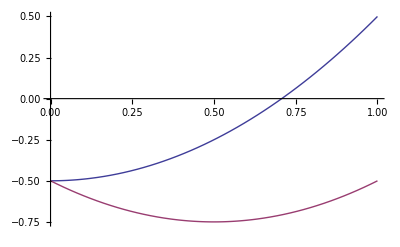

```mathematica
Plot[{-1/2+S^2,-1/2+S^2-S},{S,0,1}]
```